## Import

```mathematica
SetDirectory["C:/Users/MaeLSTRoM/Desktop/arcalive"];
```

```mathematica
datafile="아카라이브 (Responses).csv";
import=Import[datafile,"Data"];
```

```mathematica
data=import⟦2;;⟧;
label=import⟦1⟧;
```

## Simple stats

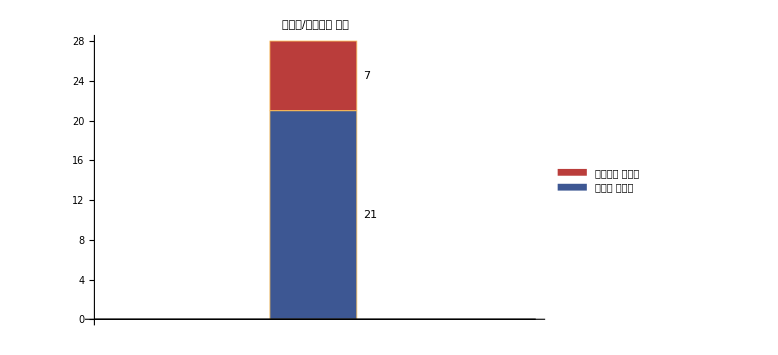

```mathematica
login=SortBy[Tally@data⟦;;,2⟧,First];
loginfig=BarChart[login⟦;;,2⟧,ChartLegends->login⟦;;,1⟧,LabelingFunction->After,ChartLayout->"Stacked",PlotLabel->"로그인/비로그인 분포",ImageSize->Large,ChartStyle->"DarkRainbow"]
```

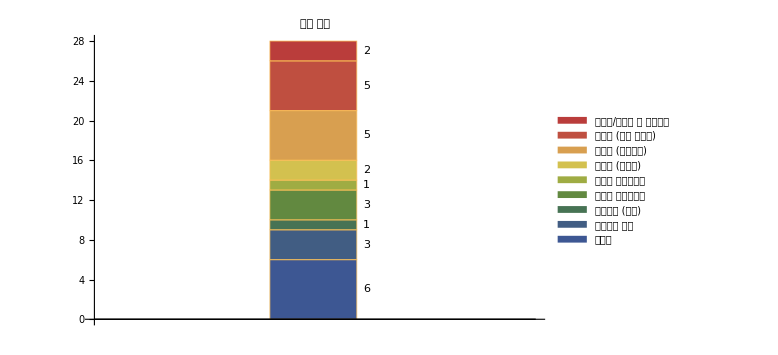

```mathematica
position=SortBy[Tally@data⟦;;,3⟧,First];
positionfig=BarChart[position⟦;;,2⟧,ChartLegends->position⟦;;,1⟧,LabelingFunction->After,ChartLayout->"Stacked",PlotLabel->"직업 분포",ImageSize->Large,ChartStyle->"DarkRainbow"]
```

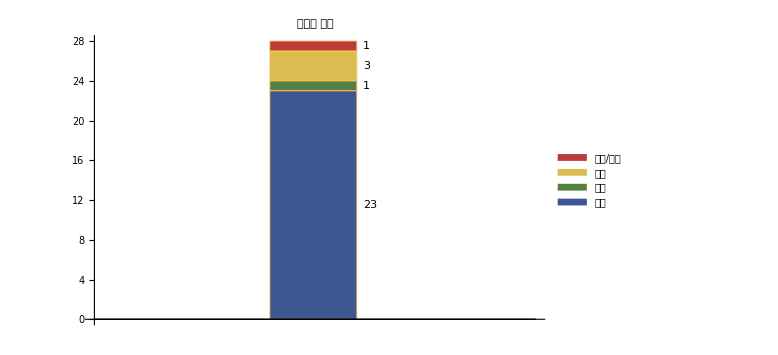

```mathematica
geographic=SortBy[Tally@data⟦;;,4⟧,First];
geografig=BarChart[geographic⟦;;,2⟧,ChartLegends->geographic⟦;;,1⟧,LabelingFunction->After,ChartLayout->"Stacked",PlotLabel->"지리적 분포",ImageSize->Large,ChartStyle->"DarkRainbow"]
```

```mathematica
topic=SortBy[Tally@Flatten@StringSplit[data⟦;;,5⟧,", "],N[#⟦2⟧]&];
topic=Callout[#⟦2⟧,#⟦1⟧]&/@topic;
tofig=BarChart[topic,BarOrigin->Left,LabelingFunction->Right,PlotLabel->ToString@Row@{"관심분야 (총 응답자 ",Length@data,")"},AspectRatio->1.3,ImageSize->Large,ChartStyle->{"Rainbow"}]
```

-Graphics-

```mathematica
topic
```

{Callout[1,플라즈마 물리학],Callout[1,원자 /분자/광 물리학 (AMO)],Callout[2,물리교육학],Callout[2,원자/분자/광 물리학 (AMO)],Callout[3,생물리학],Callout[3,화학물리학],Callout[4,핵물리학],Callout[4,천체물리학],Callout[4,반도체물리학],Callout[4,고에너지 물리학],Callout[4,양자중력/끈이론],Callout[5,천문학],Callout[5,응집물리학],Callout[5,통계물리학],Callout[6,수리물리학],Callout[6,전산물리학],Callout[7,고체물리학],Callout[8,입자물리학],Callout[9,기타 관련 공학 (양자컴퓨터/재료공학/전자공학/유체역학 등)],Callout[18,기초 물리학 (고교/대학 교육과정)]}

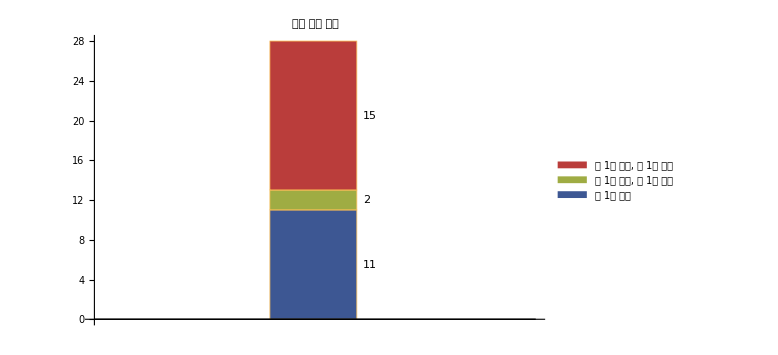

```mathematica
usage=SortBy[Tally@data⟦;;,6⟧,First];
usagefig=BarChart[usage⟦;;,2⟧,ChartLegends->usage⟦;;,1⟧,LabelingFunction->After,ChartLayout->"Stacked",PlotLabel->"평균 방문 횟수",ImageSize->Large,ChartStyle->"DarkRainbow"]
```

## 2D stats

```mathematica
topicbygroup={};
Do[
temp=SortBy[Tally@Flatten@StringSplit[everyone⟦i,;;,2⟧,", "],N[#⟦2⟧]&];
temp=Callout[#⟦2⟧,#⟦1⟧]&/@temp;
AppendTo[topicbygroup,temp];
,{i,1,Length@everyone}]
labels={ToString@Row@{"고등학생 (",Length@everyone⟦1⟧,")"},ToString@Row@{"학부생 (",Length@everyone⟦2⟧,")"},ToString@Row@{"대학원생 (",Length@everyone⟦3⟧,")"},ToString@Row@{"사람 (",Length@everyone⟦4⟧,")"}};
topicbygroupfig=BarChart[topicbygroup,BarOrigin->Left,LabelingFunction->Right,ChartLabels->{labels,None},ChartLayout->"Grouped",PlotLabel->"관심분야",AspectRatio->4,ImageSize->650,ChartStyle->{"DarkRainbow"}]
```

-Graphics-

## Export figs

```mathematica
season="3Q21";
```

```mathematica
Export[ToString@Row@{"loginfig",season,".png"},loginfig];Export[ToString@Row@{"positionfig",season,".png"},positionfig];Export[ToString@Row@{"geografig",season,".png"},geografig];Export[ToString@Row@{"tofig",season,".png"},tofig];Export[ToString@Row@{"usagefig",season,".png"},usagefig];
Export[ToString@Row@{"topicbygroupfig",season,".png"},topicbygroupfig];
```